```mathematica
SetDirectory["D:/Физика-матем/Всеукры 2007-17/2017 Кривой Рог/Proposals"]
```

D:\Физика-матем\Всеукры 2007-17\2017 Кривой Рог\Proposals

```mathematica
FileNames["*.svg"]
```

{Harmonic_partials_on_strings.svg}

```mathematica
Import[%[[1]]]
```

Import::fmtnosup: SVG is not a supported Import format.

$Failed

```mathematica
Export["string.bmp",-Graphics-]
```

string.bmp

```mathematica
Export["ac1.bmp",-Graphics-]
```

ac1.bmp

```mathematica
(U-ϕ)/R/.%122[[2]]
```

(U+1/2 (β^2/r-(β √(4 r u+β^2))/r))/R

```mathematica
(Subscript[U, 0] √2)/ω NIntegrate[((-R+√(R^2+4 Subscript[U, 0] √2 αsinϕ))/(2α)+(2 Subscript[U, 0] R √2 sinϕ+β^2-β √(4 Subscript[U, 0] √2 Rsinϕ+β^2))/(2 R^2))sinϕ/.R->300/.α->100/.β->240/.Subscript[U, 0]->4,{ϕ,0,π}]/.Subscript[U, 0]->4/.ω->100π
```

0.000543206

```mathematica
% 50
```

2.40631

```mathematica
%169/.R->300/.α->100/.β->240/.Subscript[U, 0]->36.
```

{{φ→-465.834-233.638 ⅈ},{φ→-465.834+233.638 ⅈ},{φ→4.41857},{φ→159.249}}

```mathematica
Solve[√(φ/α)+φ^2/β^2==(2(Subscript[U, 0]-φ))/R,φ];
```

```mathematica
%1/.α->12500/.β->2000/.Subscript[U, 0]->5/.R->12500.
```

{{φ→-994.287-907.545 ⅈ},{φ→-994.287+907.545 ⅈ},{φ→0.0079745},{φ→708.565}}

```mathematica
φ √(φ/α)/.%4/.α->12500
```

{-395.65+196.55 ⅈ,-395.65-196.55 ⅈ,6.36943×10^-6,168.7}

```mathematica
φ^3/β^2/.%4/.β->2000
```

{368.46-486.031 ⅈ,368.46+486.031 ⅈ,1.2678×10^-13,88.9364}

```mathematica
Export["ac2.bmp",-Graphics-]
```

ac2.bmp

```mathematica
Solve[√(ϕ/α)==(u-ϕ)/r,ϕ]
```

{{ϕ→1/2 (2 u+r^2/α-(r √(r^2+4 u α))/α)},{ϕ→1/2 (2 u+r^2/α+(r √(r^2+4 u α))/α)}}

```mathematica
Solve[ϕ^2/β^2==(u-ϕ)/r,ϕ]
```

{{ϕ→1/2 (-β^2/r-(β √(4 r u+β^2))/r)},{ϕ→1/2 (-β^2/r+(β √(4 r u+β^2))/r)}}

```mathematica
{1/2 (2 u+r^2/α-(r √(r^2+4 u α))/α),1/2 (-β^2/r+(β √(4 r u+β^2))/r)}/.β->240./.r->300./.α->100.
```

{1/2 (900.+2 u-3. √(90000.+400. u)),1/2 (-192.+0.8 √(57600.+1200. u))}

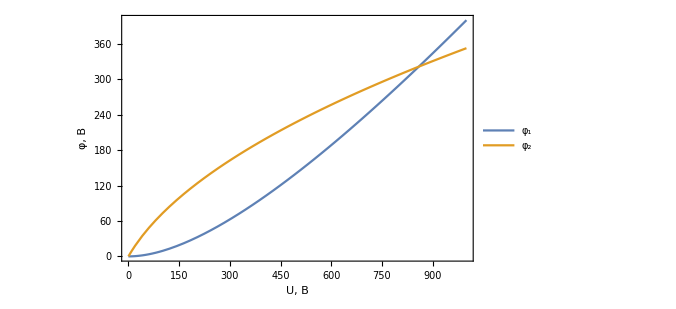

```mathematica
Plot[{1/2 (900.+2 u-3. √(90000.+400. u)),1/2 (-192.+0.8 √(57600.+1200. u))},{u,0,1000},Axes->False,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},PlotRange->{{0,1000},{0,400}},FrameStyle->Black,ImageSize->500,FrameTicksStyle->Directive[16,Black,FontFamily->"TimesNewRoman"],FrameLabel->{Style["U, В",24,Black,FontFamily->"Times New Roman"],Style["φ, В",24,Black,FontFamily->"Times New Roman"]},PlotLegends->Placed[{Style["φ_1",24,Black,FontFamily->"TimesNewRoman"],Style["φ_2",24,Black,FontFamily->"TimesNewRoman"]},{Left,Top}]]
```

```mathematica
Export["potentials.bmp",%145]
```

potentials.bmp

```mathematica
3 36^2/2/300
```

162/25

```mathematica
N[162/25]
```

6.48

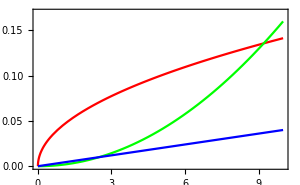

```mathematica
Plot[{√(u/500),u^2/625,u/250},{u,0,10},Axes->False,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},PlotRange->{{0,10},{0,0.17}},PlotStyle->{{Red},{Green},{Blue}},FrameStyle->Black,ImageSize->300]
```

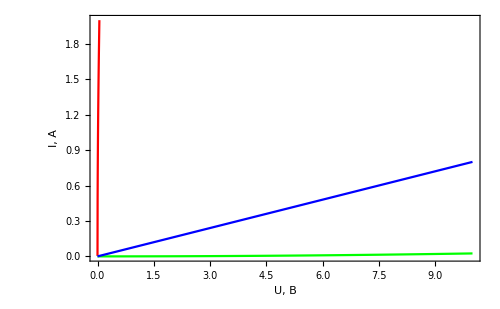

```mathematica
Plot[{1000 √(u/12500),1000 u^2/2000^2,u/12.5},{u,0,10},Axes->False,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},PlotRange->{{0,10},{0,2}},PlotStyle->{{Red},{Green},{Blue}},FrameStyle->Black,ImageSize->500,FrameTicksStyle->Directive[16,Black,FontFamily->"TimesNewRoman"],FrameLabel->{Style["U, В",24,Black,FontFamily->"Times New Roman"],Style["I, мА",24,Black,FontFamily->"Times New Roman"]}]
```

```mathematica
Export[""]
```

Plot::invpr: Value of option PlotRange is not compatible with the option ScalingFunctions -> {{Identity,Identity},{Log,Exp}}

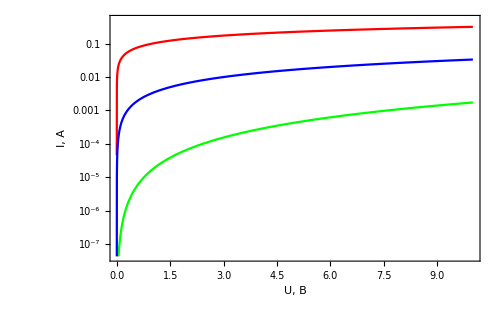

```mathematica
LogPlot[{√(u/100),u^2/240^2,u/300},{u,0,10},Axes->False,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},PlotRange->{{0.01,10},{0,0.5}},PlotStyle->{{Red},{Green},{Blue}},FrameStyle->Black,ImageSize->500,FrameTicksStyle->Directive[16,Black,FontFamily->"TimesNewRoman"],FrameLabel->{Style["U, В",24,Black,FontFamily->"Times New Roman"],Style["I, А",24,Black,FontFamily->"Times New Roman"]}]
```

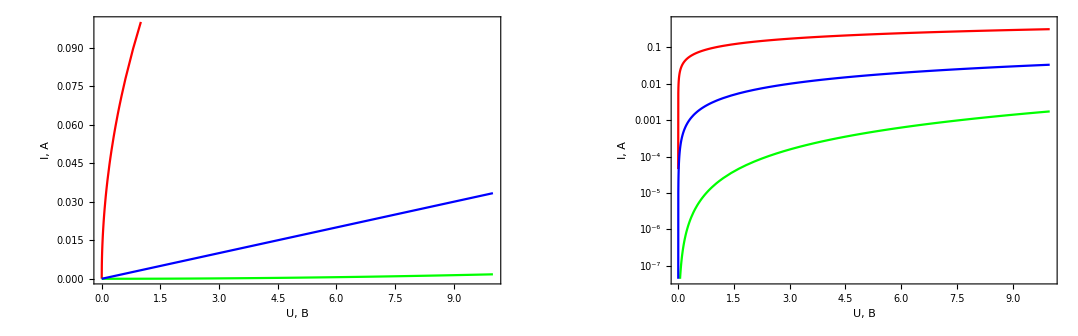

```mathematica
GraphicsGrid[{{%9,%13}}]
```

```mathematica
Export["ivcurveac.bmp",%14]
```

ivcurveac.bmp

```mathematica
Rasterize[%50,ImageResolution->300]
```

```mathematica
Export["ivcurveac.bmp",-Graphics-]
```

ivcurveac.bmp

```mathematica
Export["easy.bmp",-Graphics-]
```

easy.bmp

```mathematica
NSolve[√(x/12500)+x^2/2000^2==(5-x)/12500,x]
```

{{x→-762.335+931.06 ⅈ},{x→-762.335-931.06 ⅈ},{x→0.0019984}}

```mathematica
1000x/.%56[[3]]
```

1.9984

```mathematica
2 5^2/12500.
```

0.004

```mathematica
(%57)/1000 √((%57)/(1000 500))
```

3.99521×10^-6

```mathematica
(%57^3)/(10^9 2000^2)
```

1.99521×10^-15

```mathematica
(5-%57/1000)^2/12500
```

0.0019984

```mathematica
%58+%59+2%61
```

0.0040008

```mathematica
D[Log[√((1+Cos[x])/Sin[x])]-Cos[x]/(2 Sin[x]^2),x]//Simplify
```

Cot[x]^2 Csc[x]

```mathematica
FullSimplify[%75,b>a>0]
```

(√(-a^2+b^2))/(a+b Cos[x])

```mathematica
21,23,27,28,29,30,35,36,37,41,42,49,
```

```mathematica
{√(u α),β^2/u,r}/.u->4/.β->240./.r->300./.α->100.
```

{20.,14400.,300.}

```mathematica
√(1500 36.)
```

232.379

```mathematica
N[5 √(5/3)]
```

6.45497

```mathematica
{√(u α),β^2/u,r}/.u->5/.β->2000./.r->12500./.α->12500.
```

{250.,800000.,12500.}

```mathematica
√(125000/5)
```

50 √10

```mathematica
2 0.05^2/250
```

0.00002

```mathematica
% 10^6
```

20.

```mathematica
(β/α)^(2/3)(r+α^(1/3)β^(2/3))/.β->125./.r->750./.α->1000.
```

250.

```mathematica
(%25[[3]]+%23)50
```

0.0794033

```mathematica
%/80-1
```

-0.999007

```mathematica
(2 Subscript[U, 0] √2)/ωR NIntegrate[(Subscript[U, 0] √2 sinϕ-φ)sinϕ/.%21/.R->300/.α->100/.β->240/.Subscript[U, 0]->4,{ϕ,0,π}]/.Subscript[U, 0]->4/.ω->100π/.R->300
```

{0.109046+0.0588315 ⅈ,0.109046-0.0588315 ⅈ,0.00104486,-0.0304847}

```mathematica
(%166+%179)/0.02
```

6.12236

```mathematica
6.48-6.12
```

0.36

```mathematica
%181/6.12
```

0.0588235

```mathematica
(1.5 4^2)/300
```

0.08